## Mathematical Methods Sheet 3 CO Solutions

(a)

```mathematica
Clear[x, n];

(*Define Hermite polynomials using Rodrigues' formula*)
rodrigues[n_Integer, x_] := (-1)^n Exp[x^2] D[Exp[-x^2], {x, n}];

(*Display the first five Hermite polynomials and compare with Mathematica's build-in Hermite polynomials*)
Table[
 {k, Expand[rodriquesH[k, x]], HermiteH[k, x], FullSimplify[rodriquesH[k, x] == HermiteH[k, x]]}, {k, 0, 4}
 ]
 
 (* Check the Hermite differential equation for the first five polynomials*)
 Table[
   FullSimplify[
     D[HermiteH[k, x], {x, 2}] - 2 x D[HermiteH[k, x],x] + 2 k HermiteH[k,x]
   ], {k, 0, 4}
 ]
```

{{0,rodriquesH[0,x],1,rodriquesH[0,x]==1},{1,rodriquesH[1,x],2 x,2 x==rodriquesH[1,x]},{2,rodriquesH[2,x],-2+4 x^2,4 x^2==2+rodriquesH[2,x]},{3,rodriquesH[3,x],-12 x+8 x^3,8 x^3==12 x+rodriquesH[3,x]},{4,rodriquesH[4,x],12-48 x^2+16 x^4,12+16 x^2 (-3+x^2)==rodriquesH[4,x]}}

{0,0,0,0,0}

For orthogonality,

```mathematica
(* Build the finite orthogonality matrix*)

Table[
  FullSimplify[
    Integrate[
    Exp[-x^2] HermiteH[m, x] HermiteH[n, x], {x, -Infinity, Infinity}, Assumptions -> Element[x, Reals]
    ]
  ],
  {m, 0, 4}, {n, 0, 4}
]
```

{{√π,0,0,0,0},{0,2 √π,0,0,0},{0,0,8 √π,0,0},{0,0,0,48 √π,0},{0,0,0,0,384 √π}}

For  , the series is ,

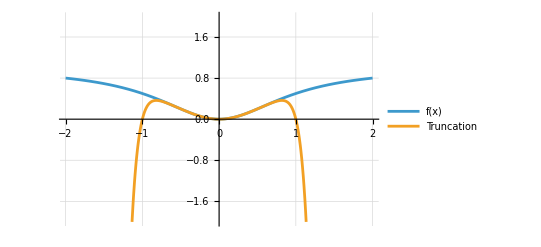

```mathematica
(* Define the function and its six-term Taylor truncation about x = 0*)
f[x_] := x^2/(1 + x^2);
fTruncated[x_] := Sum[(-1)^(k - 1) x^(2 k), {k, 1, 6}];

(*Plot these two curves*)
Plot[
  {f[x], fTruncated[x]}, {x, -2, 2},
  PlotRange -> {-2, 2}, PlotLegends -> {"f(x)", "Truncation"}, GridLines -> Automatic
]
```

(b) The generating function of Hermite polynomials is
.
Thus is the -th derivative with respect to t,

```mathematica
Clear[t];

(* Extract H_n(x) from the generating function for n = 0, 1, 2, 3, 4 *)
Table[Expand[D[Exp[2 x t - t^2], {t, k}] /. t -> 0], {k, 0, 4}]
```

{1,2 x,-2+4 x^2,-12 x+8 x^3,12-48 x^2+16 x^4}